# Complete Example

```mathematica
data1=Table[a^2, {a, 1, 20}]
```

{1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400}

## Plot the data

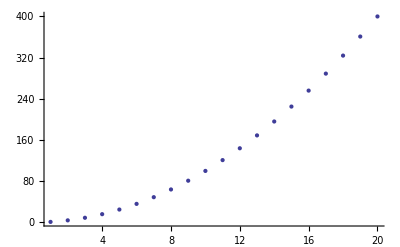

```mathematica
pldata1 = ListPlot[data1]
```

## Fit the data

```mathematica
fitdata1 = Fit[data1,{1,x},x]
```

21. x-77.

## Plot the fit

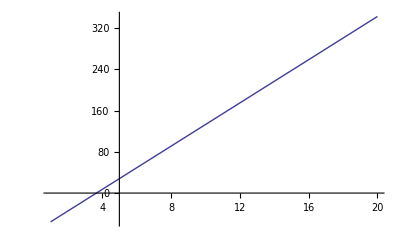

```mathematica
plotfitdata1 = Plot[fitdata1,{x,1,20}]
```

## Combine the graphics

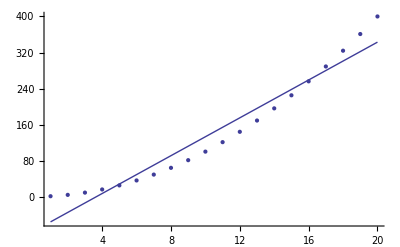

```mathematica
Show[pldata1,plotfitdata1]
```